```mathematica
data=Import["/home/tony/Workspace/local/benchmark/OH_100_3.csv"];
runs=20;
vars=9;
bytes=Table[116508*i,{i,1,9}];
totalWrite=3;
OHWrite=4;
totalRead=5;
OHRead=6;
```

```mathematica
groupedData=Partition[data,9];
```

```mathematica
writeData=Table[Mean[Table[Extract[groupedData,{i,j,totalWrite}],{i,1,runs}]],{j,1,vars}];
writeOHData=Table[Mean[Table[Extract[groupedData,{i,j,OHWrite}],{i,1,runs}]],{j,1,vars}];

writeSD=Table[StandardDeviation[Table[Extract[groupedData,{i,j,totalWrite}],{i,1,runs}]],{j,1,vars}];
writeOHSD=Table[StandardDeviation[Table[Extract[groupedData,{i,j,OHWrite}],{i,1,runs}]],{j,1,vars}];

writeTrueData=writeData-writeOHData;
writeTrueSD=writeSD-writeOHSD;

writeSpeed=(bytes*8/1000)/(writeData*10^-6);
writeTrueSpeed=(bytes*8/1000)/(writeTrueData*10^-6);

writeSpeedSD=((bytes*8/1000)*writeSD*10^-6)/(writeData*10^-6(writeData*10^-6+writeSD*10^-6));
writeTrueSpeedSD=((bytes*8/1000)*writeTrueSD*10^-6)/(writeTrueData*10^-6(writeTrueData*10^-6+writeTrueSD*10^-6));

readData=Table[Mean[Table[Extract[groupedData,{i,j,totalRead}],{i,1,runs}]],{j,1,vars}];
readOHData=Table[Mean[Table[Extract[groupedData,{i,j,OHRead}],{i,1,runs}]],{j,1,vars}];

readSD=Table[StandardDeviation[Table[Extract[groupedData,{i,j,totalRead}],{i,1,runs}]],{j,1,vars}];
readOHSD=Table[StandardDeviation[Table[Extract[groupedData,{i,j,OHRead}],{i,1,runs}]],{j,1,vars}];

readTrueData=readData-readOHData;
readTrueSD=readSD-readOHSD;

readSpeed=(bytes*8/1000)/(readData*10^-6);
readTrueSpeed=(bytes*8/1000)/(readTrueData*10^-6);

readSpeedSD=((bytes*8/1000)*readSD*10^-6)/(readData*10^-6(readData*10^-6+readSD*10^-6));
readTrueSpeedSD=((bytes*8/1000)*readTrueSD*10^-6)/(readTrueData*10^-6(readTrueData*10^-6+readTrueSD*10^-6));

writePlot=ListLinePlot[writeData,PlotStyle->Blue,PlotRange->{0,6*10^6}];
writeOHPlot=ListLinePlot[writeOHData,PlotStyle->Green,PlotRange->{0,6*10^6}];

writeSDMax=ListLinePlot[writeData+writeSD,PlotStyle->{Blue,Dashed},PlotRange->{0,6*10^6}];
writeOHSDMax=ListLinePlot[writeOHData+writeOHSD,PlotStyle->{Green,Dashed},PlotRange->{0,6*10^6}];

writeSDMin=ListLinePlot[writeData-writeSD,PlotStyle->{Blue,Dashed},PlotRange->{0,6*10^6}];
writeOHSDMin=ListLinePlot[writeOHData-writeOHSD,PlotStyle->{Green,Dashed},PlotRange->{0,6*10^6}];

writeSpeedPlot=ListLinePlot[writeSpeed,PlotStyle->Blue,PlotRange->{0,60000}];
writeTrueSpeedPlot=ListLinePlot[writeTrueSpeed,PlotStyle->Green,PlotRange->{0,60000}];

writeSpeedSDMax=ListLinePlot[writeSpeed+writeSpeedSD,PlotStyle->{Blue,Dashed},PlotRange->{0,60000}];
writeTrueSpeedSDMax=ListLinePlot[writeTrueSpeed+writeTrueSpeedSD,PlotStyle->{Green,Dashed},PlotRange->{0,60000}];

writeSpeedSDMin=ListLinePlot[writeSpeed-writeSpeedSD,PlotStyle->{Blue,Dashed},PlotRange->{0,60000}];
writeTrueSpeedSDMin=ListLinePlot[writeTrueSpeed-writeTrueSpeedSD,PlotStyle->{Green,Dashed},PlotRange->{0,60000}];

readPlot=ListLinePlot[readData,PlotStyle->Red,PlotRange->{0,6*10^6}];
readOHPlot=ListLinePlot[readOHData,PlotStyle->Orange,PlotRange->{0,6*10^6}];

readSDMax=ListLinePlot[readData+readSD,PlotStyle->{Red,Dashed},PlotRange->{0,6*10^6}];
readOHSDMax=ListLinePlot[readOHData+readOHSD,PlotStyle->{Orange,Dashed},PlotRange->{0,6*10^6}];

readSDMin=ListLinePlot[readData-readSD,PlotStyle->{Red,Dashed},PlotRange->{0,6*10^6}];
readOHSDMin=ListLinePlot[readOHData-readOHSD,PlotStyle->{Orange,Dashed},PlotRange->{0,6*10^6}];

readSpeedPlot=ListLinePlot[readSpeed,PlotStyle->Red,PlotRange->{0,60000}];
readTrueSpeedPlot=ListLinePlot[readTrueSpeed,PlotStyle->Orange,PlotRange->{0,60000}];

readSpeedSDMax=ListLinePlot[readSpeed+readSpeedSD,PlotStyle->{Red,Dashed},PlotRange->{0,60000}];
readTrueSpeedSDMax=ListLinePlot[readTrueSpeed+readTrueSpeedSD,PlotStyle->{Orange,Dashed},PlotRange->{0,60000}];

readSpeedSDMin=ListLinePlot[readSpeed-readSpeedSD,PlotStyle->{Red,Dashed},PlotRange->{0,60000}];
readTrueSpeedSDMin=ListLinePlot[readTrueSpeed-readTrueSpeedSD,PlotStyle->{Orange,Dashed},PlotRange->{0,60000}];
```

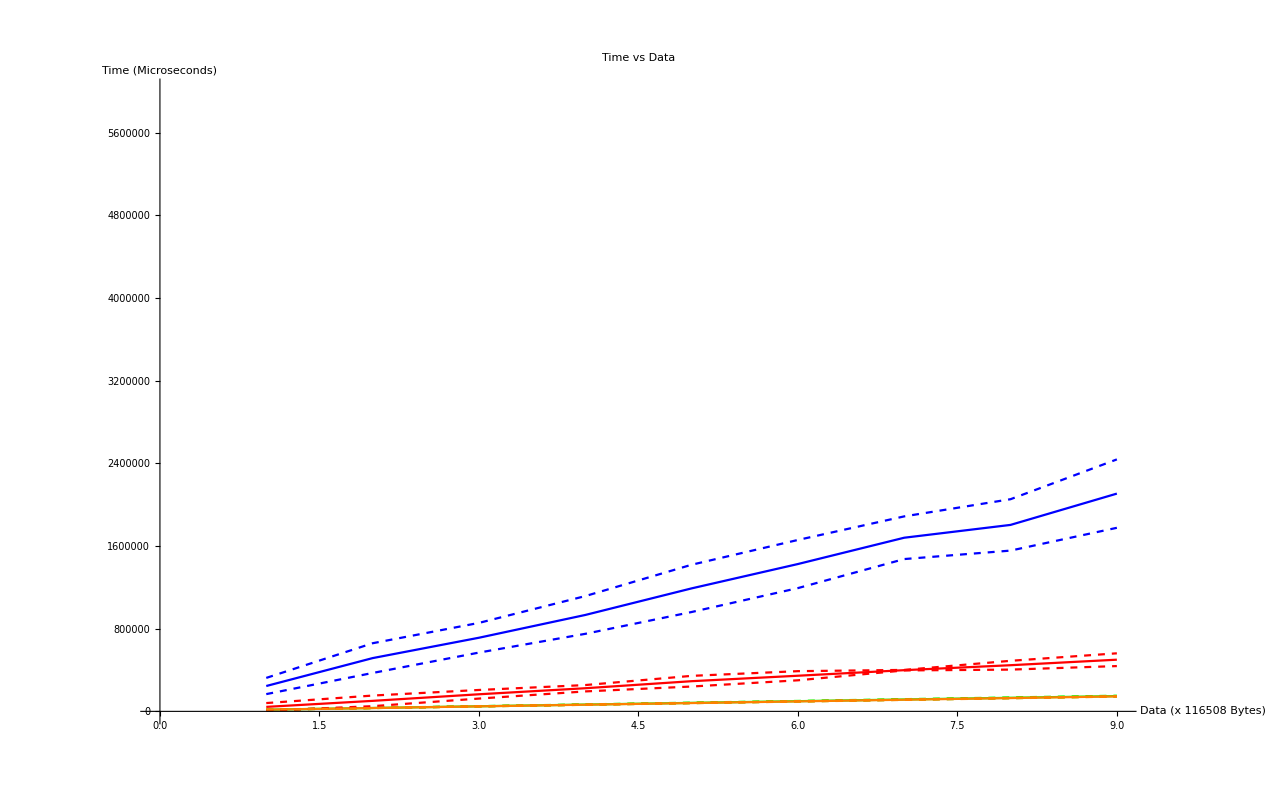

```mathematica
Show[writePlot,writeOHPlot,writeSDMax,writeOHSDMax,writeSDMin,writeOHSDMin,readPlot,readOHPlot,readSDMax,readOHSDMax,readSDMin,readOHSDMin,ImageSize->1280,AxesLabel->{HoldForm["Data (x 116508 Bytes)"],HoldForm["Time (Microseconds)"]},PlotLabel->HoldForm["Time vs Data"],LabelStyle->{GrayLevel[0]}]
```

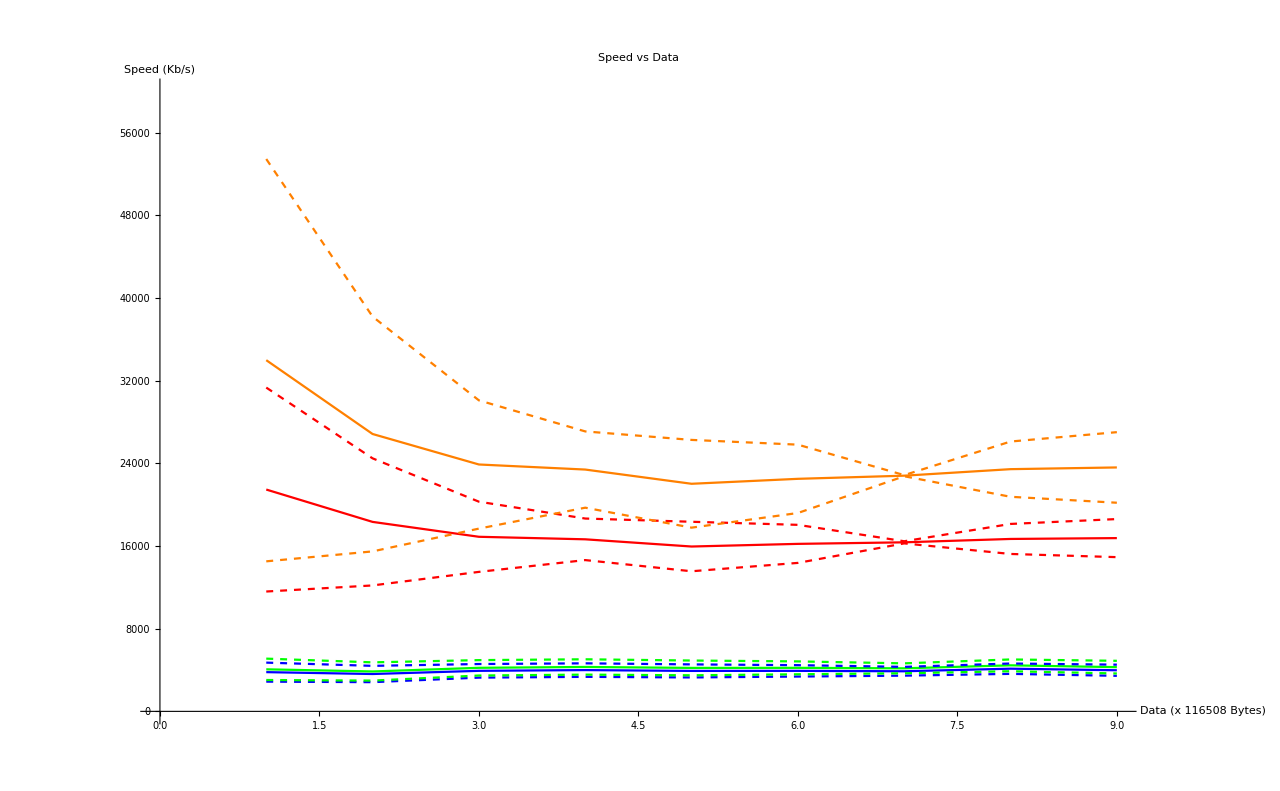

```mathematica
Show[writeSpeedPlot,writeTrueSpeedPlot,writeSpeedSDMax,writeTrueSpeedSDMax,writeSpeedSDMin,writeTrueSpeedSDMin,readSpeedPlot,readTrueSpeedPlot,readSpeedSDMax,readTrueSpeedSDMax,readSpeedSDMin,readTrueSpeedSDMin,ImageSize->1280,AxesLabel->{HoldForm["Data (x 116508 Bytes)"],HoldForm["Speed (Kb/s)"]},PlotLabel->HoldForm["Speed vs Data"],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Mean[writeSpeed]//N
```

3907.08

```mathematica
Mean[readSpeed]//N
```

17261.7